```mathematica
(*Code initially borrowed from Mike Gehm&Michael Stenner 2004 Duke Coils.nb*)
```

```mathematica
mu0=4 Pi*10^-3;(*Gives answers in Gauss*)
```

```mathematica
(*Power Density Calculation: *)
Watts = 15;
DiameterInmm = 2.5;
AreaInCmSquared = Pi*(DiameterInmm*0.1)^2;
```

```mathematica
Watts/AreaInCmSquared (*gives answer in Joules per cm^2*)
```

76.3944

```mathematica
Bz[r_,z_,coil_] := coil[[3]]*coil[[4]] * 
((mu0/(2Pi))/(√((coil[[1]]+r)^2 + (z - coil[[2]])^2))) *
(EllipticK[(4coil[[1]]r)/((coil[[1]] + r)^2 + (z - coil[[2]])^2)] +
((coil[[1]]^2 - r^2 - (z - coil[[2]])^2 )/((coil[[1]] - r)^2 + (z-coil[[2]])^2))*
EllipticE[(4coil[[1]]r)/((coil[[1]] + r)^2 + (z-coil[[2]])^2)])
```

```mathematica
Br[r_,z_,coil_] := coil[[3]]*coil[[4]]*
(z-coil[[2]])*(mu0/(2 Pi r))/(√((coil[[1]] + r)^2+ (z-coil[[2]])^2))*
(-EllipticK[(4 coil[[1]] r)/((coil[[1]]+r)^2+ (z-coil[[2]])^2)]+
((coil[[1]]^2+ r^2+(z-coil[[2]])^2)/((coil[[1]] - r)^2+(z-coil[[2]])^2))*
EllipticE[(4 coil[[1]] r)/((coil[[1]]+r)^2+ (z-coil[[2]])^2)])
```

```mathematica
AxialField[r_,z_,coils_]:=
Module[{},TempFunc[coil_]:=Bz[r,z,coil];
	Plus @@Map[TempFunc,coils,{1}]]
```

```mathematica
RadialField[r_,z_,coils_]:=
Module[{},TempFunc[coil_]:=Br[r,z,coil];
	Plus @@Map[TempFunc,coils,{1}]]
```

```mathematica
FieldMag[r_,z_,coils_]:= If[r==0,AxialField[r,z,coils],
√(AxialField[r,z,coils]^2+RadialField[r,z,coils]^2)]
```

```mathematica
(*coils: {r,z,turns,current}*)
```

```mathematica
ExampleCoils = {{.1,.05,80,-.001},{.1,-.05,80,.001}};
```

```mathematica
ExampleCoils[[1,2]]
```

0.05

```mathematica
WaterHolePercentage = (0.0015875^2)/(0.003175^2)
```

0.25

```mathematica
CoilSliceArea = (0.003175^2)-(0.0015875^2)
```

7.56047×10^-6

```mathematica
CoilBankSliceArea = CoilSliceArea*51
```

0.000385584

```mathematica
VolumeWithHoles = CoilBankSliceArea*(2*Pi*0.045)
```

0.000109021

```mathematica
VolumeofCoilBank = 0.030*((Pi 0.055^2) - (Pi 0.035^2))
```

0.000169646

```mathematica
VolumeafterExpansion = VolumeWithHoles(1+3*(17*10^-6)*10) (*For 10 degree change*)
```

0.000109077

```mathematica
PercentVolumeChange = (VolumeafterExpansion/VolumeWithHoles-1)*100
```

0.051

```mathematica
LithiumLabCoilTotal = {{.045,.0325,51,111},{.045,-.0325,51,111}};
LithiumLabCoilExpanded= {{.045*1.0005,.0325,51,111},{.045*1.0005,-.0325,51,111}};
LithiumLabCoilArray = {{}};
```

```mathematica
FieldMag[0,0,LithiumLabCoilTotal]
```

842.243

```mathematica
FieldMag[0,0,LithiumLabCoilExpanded] (*0.05% shift; assume max displacement*)
```

842.255

```mathematica
Out[244]-Out[243]
```

-%243+%244

```mathematica
(*Plot[AxialField[0,z,LithiumLabCoilTotal],{z,-.045,.045}]*)
```

```mathematica
(*Plot[RadialField[0.01,z,LithiumLabCoilTotal],{z,-.04,.04}]*)
```

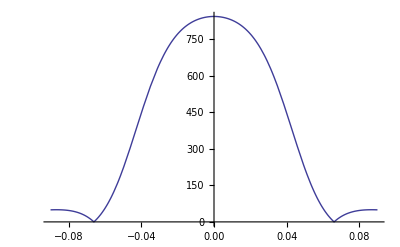

```mathematica
Plot[FieldMag[r,0,LithiumLabCoilTotal],{r,-.09,.09}]
```

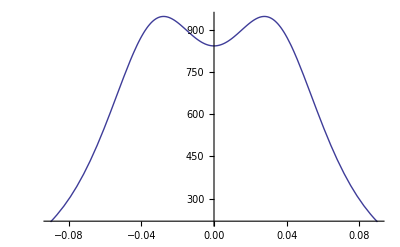

```mathematica
Plot[FieldMag[0,z,LithiumLabCoilTotal],{z,-.09,.09}]
```

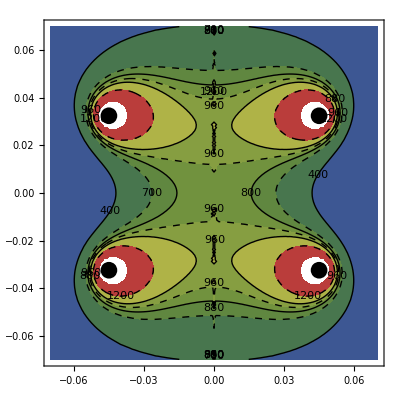

```mathematica
Show[ContourPlot[FieldMag[r,z,LithiumLabCoilTotal],{r,-.070,.070},{z,-.07,.07},Contours->{400,700,800,880,960,1200},ColorFunction->"DarkRainbow",ContourLabels->True,ContourStyle->{Black,Directive[Black,Dashed]}],Graphics[{PointSize[0.03],{Point[{{LithiumLabCoilTotal[[1,1]],LithiumLabCoilTotal[[1,2]]},{-LithiumLabCoilTotal[[1,1]],-LithiumLabCoilTotal[[1,2]]},{LithiumLabCoilTotal[[1,1]],-LithiumLabCoilTotal[[1,2]]},{-LithiumLabCoilTotal[[1,1]],LithiumLabCoilTotal[[1,2]]}}]}}]]
```

```mathematica
ContourPlot3D[FieldMag[Sqrt[x^2 + y^2],z,LithiumLabCoilTotal],{x,0,.050},{y,-.050,.050},{z,-.05,.05},Contours->10,ContourStyle->Table[Hue[i/7],{i,0,6}],Mesh->None]
```

$Aborted

```mathematica
(* 10.2 Version... SliceContourPlot3D[FieldMag[Sqrt[x^2 + y^2],z,ExampleCoils],"CenterPlanes",{x,-.2,.2},{y,-.2,.2},{z,-.2,.2}] *)
```

```mathematica
VectorPlot3D[FieldMag[√(x^2+ y^2),z,ExampleCoils],{x,-.3,.3},{y,-.3,.3},{z,-.1,.1}]
```

Part::partw: Part 1 of {} does not exist.

```mathematica
Plot3D[FieldMag[√(x^2+ y^2),z,ExampleCoils],{x,-.2,.2},{y,-.2,.2}]
```